```mathematica
ClearAll["Global`*"];
{t0,tn}= {0.0, 2.0}; n=2; t=t0; h:=0.01;a=-2;b=4;eps=0.01;
(* u – массив для хранения текущих значений решений;
v – то же для значений, полученных на предыдущем шаге;
p – массив для хранения значений правых частей *)
Array[u,n,1];Array[v,n,1];Array[p,n,1];Array[q,n,1];
(* Начальные условия *)
w0={x0,y0}={a+eps,b};
(* Списки приближенных значений *)
xlst=List[{t0,x0}];ylst=List[{t0,y0}];xylst=List[{x0,y0}];
For[i=1,i≤n,i++,u[i]=w0[[i]];v[i]=u[i]];
(* Вспомогательная функция для вычисления значений правых частей *)
fp[t_,h_,u_][p_]:=Block[{x=u[1],y=u[2]},p[1]=h(x^2-y);p[2]=h (x^2-(y-2)^2);]
(* По формулам формируем таблицы (списки) приближенных значений неизвестных функций *)
m=(tn-t0)/h+1; (* m - количество узлов *)
For[i=1,i≤m,i++, (* вычисление значений приближенных решений *) 
fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=p[k];u[k]=v[k]+p[k]/2];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]/2];fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,u[k]=v[k]+(q[k]+p[k])/6;v[k]=u[k]];{x,y}={v[1],v[2]};
(* Списки значений неизвестных функций *)
xlst=Append[xlst,{t,x}];ylst=Append[ylst,{t,y}];xylst=Append[xylst,{x,y}]];
(* Графики формируем так же, как в предыдущем примере. Сначала строим интегральные кривые, представленные таблицами Subscript[x, i]=x(Subscript[t, i]), Subscript[y, i]=y(Subscript[t, i]),Subscript[z, i]=z(Subscript[t, i]) *)

lst11={Automatic,AbsoluteThickness[2],AbsoluteDashing[{4,4}],RGBColor[0,0,1]};
gr11=ListLinePlot[xlst,PlotStyle->lst10,PlotRange -> {-10,10}];
gr12=ListLinePlot[ylst,PlotStyle->lst11,PlotRange -> {-10,10}];
(* Затем строим фазовую траекторию, состоящую из точек (Subscript[x, i],Subscript[y, i],Subscript[z, i]) *)
tab1=Table[Point[xylst[[i]]],{i,1,m}];
gr1=Graphics[tab1];

Show[gr1,Axes->True,PlotRange -> All]
```

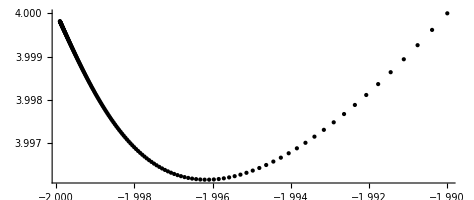
```mathematica
-Graphics-
(*второй для первой *)
{t0,tn}= {0.0, 2.0}; n=2; t=t0; h:=0.01;a=-2;b=4;eps=0.01;
(* u – массив для хранения текущих значений решений;
v – то же для значений, полученных на предыдущем шаге;
p – массив для хранения значений правых частей *)
Array[u,n,1];Array[v,n,1];Array[p,n,1];Array[q,n,1];
(* Начальные условия *)
w0={x0,y0}={a-eps,b};
(* Списки приближенных значений *)
xlst=List[{t0,x0}];ylst=List[{t0,y0}];xylst=List[{x0,y0}];
For[i=1,i≤n,i++,u[i]=w0[[i]];v[i]=u[i]];
(* Вспомогательная функция для вычисления значений правых частей *)
fp[t_,h_,u_][p_]:=Block[{x=u[1],y=u[2]},p[1]=h(x^2-y);p[2]=h (x^2-(y-2)^2);]
(* По формулам формируем таблицы (списки) приближенных значений неизвестных функций *)
m=(tn-t0)/h+1; (* m - количество узлов *)
For[i=1,i≤m,i++, (* вычисление значений приближенных решений *) 
fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=p[k];u[k]=v[k]+p[k]/2];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]/2];fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,u[k]=v[k]+(q[k]+p[k])/6;v[k]=u[k]];{x,y}={v[1],v[2]};
(* Списки значений неизвестных функций *)
xlst=Append[xlst,{t,x}];ylst=Append[ylst,{t,y}];xylst=Append[xylst,{x,y}]];
(* Графики формируем так же, как в предыдущем примере. Сначала строим интегральные кривые, представленные таблицами Subscript[x, i]=x(Subscript[t, i]), Subscript[y, i]=y(Subscript[t, i]),Subscript[z, i]=z(Subscript[t, i]) *)

lst11={Automatic,AbsoluteThickness[2],AbsoluteDashing[{4,4}],RGBColor[0,0,1]};
gr11=ListLinePlot[xlst,PlotStyle->lst10,PlotRange -> {-10,10}];
gr12=ListLinePlot[ylst,PlotStyle->lst11,PlotRange -> {-10,10}];
(* Затем строим фазовую траекторию, состоящую из точек (Subscript[x, i],Subscript[y, i],Subscript[z, i]) *)
tab1=Table[Point[xylst[[i]]],{i,1,m}];
gr2=Graphics[tab1];

Show[gr2,Axes->True,PlotRange -> All]
```

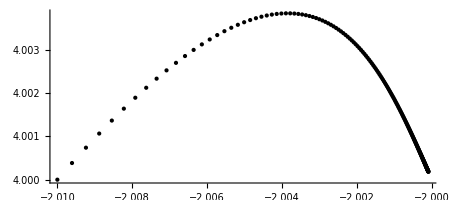
```mathematica
-Graphics-
(*третий для первой *)
{t0,tn}= {0.0, 2.0}; n=2; t=t0; h:=0.01;a=-2;b=4;eps=0.01;
(* u – массив для хранения текущих значений решений;
v – то же для значений, полученных на предыдущем шаге;
p – массив для хранения значений правых частей *)
Array[u,n,1];Array[v,n,1];Array[p,n,1];Array[q,n,1];
(* Начальные условия *)
w0={x0,y0}={a,b+eps};
(* Списки приближенных значений *)
xlst=List[{t0,x0}];ylst=List[{t0,y0}];xylst=List[{x0,y0}];
For[i=1,i≤n,i++,u[i]=w0[[i]];v[i]=u[i]];
(* Вспомогательная функция для вычисления значений правых частей *)
fp[t_,h_,u_][p_]:=Block[{x=u[1],y=u[2]},p[1]=h(x^2-y);p[2]=h (x^2-(y-2)^2);]
(* По формулам формируем таблицы (списки) приближенных значений неизвестных функций *)
m=(tn-t0)/h+1; (* m - количество узлов *)
For[i=1,i≤m,i++, (* вычисление значений приближенных решений *) 
fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=p[k];u[k]=v[k]+p[k]/2];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]/2];fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,u[k]=v[k]+(q[k]+p[k])/6;v[k]=u[k]];{x,y}={v[1],v[2]};
(* Списки значений неизвестных функций *)
xlst=Append[xlst,{t,x}];ylst=Append[ylst,{t,y}];xylst=Append[xylst,{x,y}]];
(* Графики формируем так же, как в предыдущем примере. Сначала строим интегральные кривые, представленные таблицами Subscript[x, i]=x(Subscript[t, i]), Subscript[y, i]=y(Subscript[t, i]),Subscript[z, i]=z(Subscript[t, i]) *)

lst11={Automatic,AbsoluteThickness[2],AbsoluteDashing[{4,4}],RGBColor[0,0,1]};
gr11=ListLinePlot[xlst,PlotStyle->lst10,PlotRange -> {-10,10}];
gr12=ListLinePlot[ylst,PlotStyle->lst11,PlotRange -> {-10,10}];
(* Затем строим фазовую траекторию, состоящую из точек (Subscript[x, i],Subscript[y, i],Subscript[z, i]) *)
tab1=Table[Point[xylst[[i]]],{i,1,m}];
gr3=Graphics[tab1];

Show[gr3,Axes->True,PlotRange -> All]
```

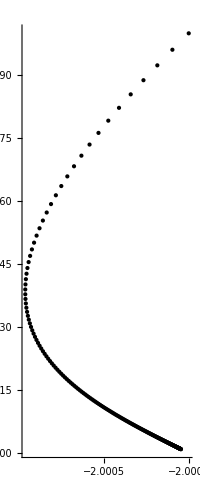

```mathematica
(*четвертый для первой *)
{t0,tn}= {0.0, 2.0}; n=2; t=t0; h:=0.01;a=-2;b=4;eps=0.01;
(* u – массив для хранения текущих значений решений;
v – то же для значений, полученных на предыдущем шаге;
p – массив для хранения значений правых частей *)
Array[u,n,1];Array[v,n,1];Array[p,n,1];Array[q,n,1];
(* Начальные условия *)
w0={x0,y0}={a,b-eps};
(* Списки приближенных значений *)
xlst=List[{t0,x0}];ylst=List[{t0,y0}];xylst=List[{x0,y0}];
For[i=1,i≤n,i++,u[i]=w0[[i]];v[i]=u[i]];
(* Вспомогательная функция для вычисления значений правых частей *)
fp[t_,h_,u_][p_]:=Block[{x=u[1],y=u[2]},p[1]=h(x^2-y);p[2]=h (x^2-(y-2)^2);]
(* По формулам формируем таблицы (списки) приближенных значений неизвестных функций *)
m=(tn-t0)/h+1; (* m - количество узлов *)
For[i=1,i≤m,i++, (* вычисление значений приближенных решений *) 
fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=p[k];u[k]=v[k]+p[k]/2];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]/2];fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,u[k]=v[k]+(q[k]+p[k])/6;v[k]=u[k]];{x,y}={v[1],v[2]};
(* Списки значений неизвестных функций *)
xlst=Append[xlst,{t,x}];ylst=Append[ylst,{t,y}];xylst=Append[xylst,{x,y}]];
(* Графики формируем так же, как в предыдущем примере. Сначала строим интегральные кривые, представленные таблицами Subscript[x, i]=x(Subscript[t, i]), Subscript[y, i]=y(Subscript[t, i]),Subscript[z, i]=z(Subscript[t, i]) *)

lst11={Automatic,AbsoluteThickness[2],AbsoluteDashing[{4,4}],RGBColor[0,0,1]};
gr11=ListLinePlot[xlst,PlotStyle->lst10,PlotRange -> {-10,10}];
gr12=ListLinePlot[ylst,PlotStyle->lst11,PlotRange -> {-10,10}];
(* Затем строим фазовую траекторию, состоящую из точек (Subscript[x, i],Subscript[y, i],Subscript[z, i]) *)
tab1=Table[Point[xylst[[i]]],{i,1,m}];
gr4=Graphics[tab1];

Show[gr4,Axes->True,PlotRange -> All]
```

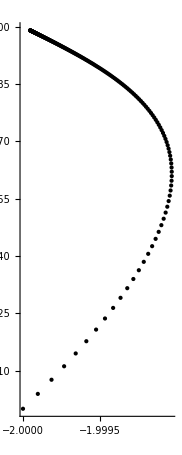
```mathematica
-Graphics-
(*первый для второй *)
```

```mathematica
{t0,tn}= {0.0, 2.0}; n=2; t=t0; h:=0.01;a=-1;b=1;eps=0.01;
(* u – массив для хранения текущих значений решений;
v – то же для значений, полученных на предыдущем шаге;
p – массив для хранения значений правых частей *)
Array[u,n,1];Array[v,n,1];Array[p,n,1];Array[q,n,1];
(* Начальные условия *)
w0={x0,y0}={a+eps,b};
(* Списки приближенных значений *)
xlst=List[{t0,x0}];ylst=List[{t0,y0}];xylst=List[{x0,y0}];
For[i=1,i≤n,i++,u[i]=w0[[i]];v[i]=u[i]];
(* Вспомогательная функция для вычисления значений правых частей *)
fp[t_,h_,u_][p_]:=Block[{x=u[1],y=u[2]},p[1]=h(x^2-y);p[2]=h (x^2-(y-2)^2);]
(* По формулам формируем таблицы (списки) приближенных значений неизвестных функций *)
m=(tn-t0)/h+1; (* m - количество узлов *)
For[i=1,i≤m,i++, (* вычисление значений приближенных решений *) 
fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=p[k];u[k]=v[k]+p[k]/2];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]/2];fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,u[k]=v[k]+(q[k]+p[k])/6;v[k]=u[k]];{x,y}={v[1],v[2]};
(* Списки значений неизвестных функций *)
xlst=Append[xlst,{t,x}];ylst=Append[ylst,{t,y}];xylst=Append[xylst,{x,y}]];
(* Графики формируем так же, как в предыдущем примере. Сначала строим интегральные кривые, представленные таблицами Subscript[x, i]=x(Subscript[t, i]), Subscript[y, i]=y(Subscript[t, i]),Subscript[z, i]=z(Subscript[t, i]) *)

lst11={Automatic,AbsoluteThickness[2],AbsoluteDashing[{4,4}],RGBColor[0,0,1]};
gr11=ListLinePlot[xlst,PlotStyle->lst10,PlotRange -> {-10,10}];
gr12=ListLinePlot[ylst,PlotStyle->lst11,PlotRange -> {-10,10}];
(* Затем строим фазовую траекторию, состоящую из точек (Subscript[x, i],Subscript[y, i],Subscript[z, i]) *)
tab1=Table[Point[xylst[[i]]],{i,1,m}];
gr5=Graphics[tab1];

Show[gr5,Axes->True,PlotRange -> All]
```

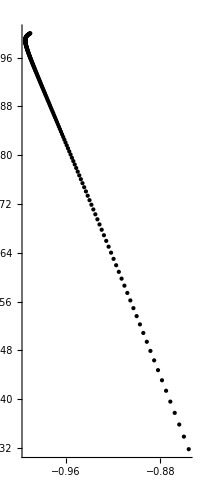

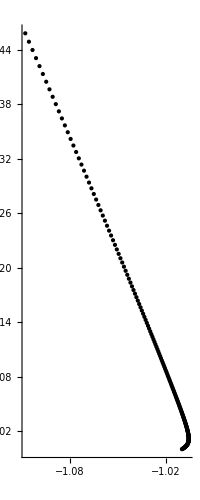

```mathematica
(*второй для второй*)
{t0,tn}= {0.0, 2.0}; n=2; t=t0; h:=0.01;a=-1;b=1;eps=0.01;
(* u – массив для хранения текущих значений решений;
v – то же для значений, полученных на предыдущем шаге;
p – массив для хранения значений правых частей *)
Array[u,n,1];Array[v,n,1];Array[p,n,1];Array[q,n,1];
(* Начальные условия *)
w0={x0,y0}={a-eps,b};
(* Списки приближенных значений *)
xlst=List[{t0,x0}];ylst=List[{t0,y0}];xylst=List[{x0,y0}];
For[i=1,i≤n,i++,u[i]=w0[[i]];v[i]=u[i]];
(* Вспомогательная функция для вычисления значений правых частей *)
fp[t_,h_,u_][p_]:=Block[{x=u[1],y=u[2]},p[1]=h(x^2-y);p[2]=h (x^2-(y-2)^2);]
(* По формулам формируем таблицы (списки) приближенных значений неизвестных функций *)
m=(tn-t0)/h+1; (* m - количество узлов *)
For[i=1,i≤m,i++, (* вычисление значений приближенных решений *) 
fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=p[k];u[k]=v[k]+p[k]/2];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]/2];fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,u[k]=v[k]+(q[k]+p[k])/6;v[k]=u[k]];{x,y}={v[1],v[2]};
(* Списки значений неизвестных функций *)
xlst=Append[xlst,{t,x}];ylst=Append[ylst,{t,y}];xylst=Append[xylst,{x,y}]];
(* Графики формируем так же, как в предыдущем примере. Сначала строим интегральные кривые, представленные таблицами Subscript[x, i]=x(Subscript[t, i]), Subscript[y, i]=y(Subscript[t, i]),Subscript[z, i]=z(Subscript[t, i]) *)

lst11={Automatic,AbsoluteThickness[2],AbsoluteDashing[{4,4}],RGBColor[0,0,1]};
gr11=ListLinePlot[xlst,PlotStyle->lst10,PlotRange -> {-10,10}];
gr12=ListLinePlot[ylst,PlotStyle->lst11,PlotRange -> {-10,10}];
(* Затем строим фазовую траекторию, состоящую из точек (Subscript[x, i],Subscript[y, i],Subscript[z, i]) *)
tab1=Table[Point[xylst[[i]]],{i,1,m}];
gr6=Graphics[tab1];

Show[gr6,Axes->True,PlotRange -> All]
```

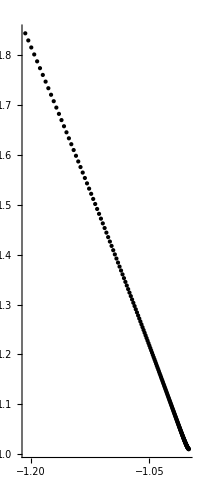

```mathematica
(*третий для второй*)
{t0,tn}= {0.0, 2.0}; n=2; t=t0; h:=0.01;a=-1;b=1;eps=0.01;
(* u – массив для хранения текущих значений решений;
v – то же для значений, полученных на предыдущем шаге;
p – массив для хранения значений правых частей *)
Array[u,n,1];Array[v,n,1];Array[p,n,1];Array[q,n,1];
(* Начальные условия *)
w0={x0,y0}={a,b+eps};
(* Списки приближенных значений *)
xlst=List[{t0,x0}];ylst=List[{t0,y0}];xylst=List[{x0,y0}];
For[i=1,i≤n,i++,u[i]=w0[[i]];v[i]=u[i]];
(* Вспомогательная функция для вычисления значений правых частей *)
fp[t_,h_,u_][p_]:=Block[{x=u[1],y=u[2]},p[1]=h(x^2-y);p[2]=h (x^2-(y-2)^2);]
(* По формулам формируем таблицы (списки) приближенных значений неизвестных функций *)
m=(tn-t0)/h+1; (* m - количество узлов *)
For[i=1,i≤m,i++, (* вычисление значений приближенных решений *) 
fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=p[k];u[k]=v[k]+p[k]/2];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]/2];fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,u[k]=v[k]+(q[k]+p[k])/6;v[k]=u[k]];{x,y}={v[1],v[2]};
(* Списки значений неизвестных функций *)
xlst=Append[xlst,{t,x}];ylst=Append[ylst,{t,y}];xylst=Append[xylst,{x,y}]];
(* Графики формируем так же, как в предыдущем примере. Сначала строим интегральные кривые, представленные таблицами Subscript[x, i]=x(Subscript[t, i]), Subscript[y, i]=y(Subscript[t, i]),Subscript[z, i]=z(Subscript[t, i]) *)

lst11={Automatic,AbsoluteThickness[2],AbsoluteDashing[{4,4}],RGBColor[0,0,1]};
gr11=ListLinePlot[xlst,PlotStyle->lst10,PlotRange -> {-10,10}];
gr12=ListLinePlot[ylst,PlotStyle->lst11,PlotRange -> {-10,10}];
(* Затем строим фазовую траекторию, состоящую из точек (Subscript[x, i],Subscript[y, i],Subscript[z, i]) *)
tab1=Table[Point[xylst[[i]]],{i,1,m}];
gr7=Graphics[tab1];

Show[gr7,Axes->True,PlotRange -> All]
```

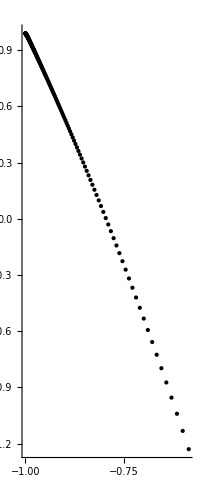

```mathematica
(*четвертый для второй*)
{t0,tn}= {0.0, 2.0}; n=2; t=t0; h:=0.01;a=-1;b=1;eps=0.01;
(* u – массив для хранения текущих значений решений;
v – то же для значений, полученных на предыдущем шаге;
p – массив для хранения значений правых частей *)
Array[u,n,1];Array[v,n,1];Array[p,n,1];Array[q,n,1];
(* Начальные условия *)
w0={x0,y0}={a,b-eps};
(* Списки приближенных значений *)
xlst=List[{t0,x0}];ylst=List[{t0,y0}];xylst=List[{x0,y0}];
For[i=1,i≤n,i++,u[i]=w0[[i]];v[i]=u[i]];
(* Вспомогательная функция для вычисления значений правых частей *)
fp[t_,h_,u_][p_]:=Block[{x=u[1],y=u[2]},p[1]=h(x^2-y);p[2]=h (x^2-(y-2)^2);]
(* По формулам формируем таблицы (списки) приближенных значений неизвестных функций *)
m=(tn-t0)/h+1; (* m - количество узлов *)
For[i=1,i≤m,i++, (* вычисление значений приближенных решений *) 
fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=p[k];u[k]=v[k]+p[k]/2];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]/2];fp[t,h,u][p];
For[k=1,k≤n,k++,q[k]=q[k]+2 p[k];u[k]=v[k]+p[k]];t=t+h/2;fp[t,h,u][p];
For[k=1,k≤n,k++,u[k]=v[k]+(q[k]+p[k])/6;v[k]=u[k]];{x,y}={v[1],v[2]};
(* Списки значений неизвестных функций *)
xlst=Append[xlst,{t,x}];ylst=Append[ylst,{t,y}];xylst=Append[xylst,{x,y}]];
(* Графики формируем так же, как в предыдущем примере. Сначала строим интегральные кривые, представленные таблицами Subscript[x, i]=x(Subscript[t, i]), Subscript[y, i]=y(Subscript[t, i]),Subscript[z, i]=z(Subscript[t, i]) *)

lst11={Automatic,AbsoluteThickness[2],AbsoluteDashing[{4,4}],RGBColor[0,0,1]};
gr11=ListLinePlot[xlst,PlotStyle->lst10,PlotRange -> {-10,10}];
gr12=ListLinePlot[ylst,PlotStyle->lst11,PlotRange -> {-10,10}];
(* Затем строим фазовую траекторию, состоящую из точек (Subscript[x, i],Subscript[y, i],Subscript[z, i]) *)
tab1=Table[Point[xylst[[i]]],{i,1,m}];
gr8=Graphics[tab1];

Show[gr8,Axes->True,PlotRange -> All]
```

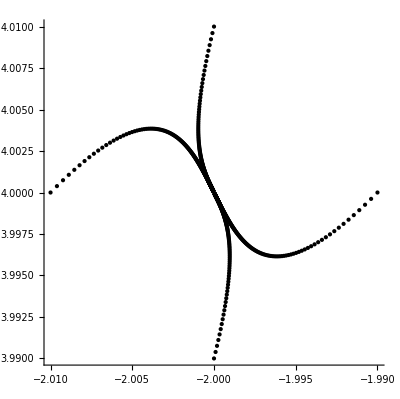

```mathematica
Show[gr1,gr2,gr3,gr4,Axes->True,PlotRange -> All]
```

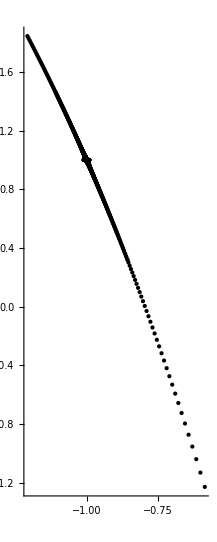

```mathematica
Show[gr5,gr6,gr7,gr8,Axes->True,PlotRange -> All]
```